```mathematica
SetGraph[form_]:=Block[{vars=ListofVars[form], edges={}},
Table[
Table[
If[SubsetQ[SymbolToSets[v1],SymbolToSets[v2]],edges=Append[edges,v1->v2]]
,{v2,Select[vars,#=!=v1&]}
]
,{v1,vars}
];
Graph[vars,edges,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]
]
```

```mathematica
MyRewrite7[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"O"]&]},
If[vars=={},
Factor[form],
Total[
Table[
v*SetGraph[Factor[Last[CoefficientList[form,v]]]],
{v,vars}
]
]
]
]
```

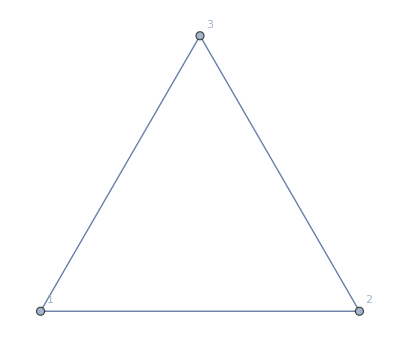
-Graphics-
{{}→{},{1}→{},{2}→{},{3}→{},{1,2}→{O3 (I1x2→I1),O3 (I1x2→I2)},{1,3}→{O2 (I1x3→I1),O2 (I1x3→I3)},{2,3}→{O1 (I2x3→I2),O1 (I2x3→I3)},{1,2,3}→I1x2x3}

```mathematica
With[{g=CycleGraph[3]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Monitor[
Table[
Framed[s->With[{form=CalculateInOutFormulaFull[g,s]},MyRewrite7[form]]
],{s,Subsets[VertexList[g]]}],
s]
}
]
]
```

```mathematica
Map[SymbolToSets,ListofVars[-6+2 I1-I1x2+I1x2x3-I1x3+2 I2-I2x3+2 I3]]
```

{{{1},{2},{3}},{{1}},{{1},{2}},{{1},{3}},{{2}},{{2},{3}},{{3}}}

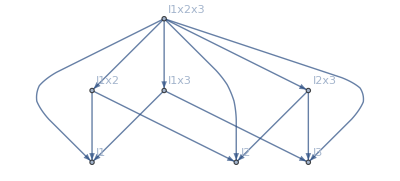

```mathematica
Graph[SetGraph[-6+2 I1-I1x2+I1x2x3-I1x3+2 I2-I2x3+2 I3],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]
```